```mathematica
Clear["Global`*"]
f[x1_,x2_]=x1^4+x2^4-2 x1^2-4x1 x2-2 x2^2;
x0={1.2,-1.};
ϵ=10^-3;
```

```mathematica
(*знайдемо мінімум за допомогою вбудованої функції*)
min=FindMinimum[f[x1,x2],{{x1,1.2},{x2,-1}}]
```

{-8.,{x1→1.41421,x2→1.41421}}

```mathematica
(*функція, яка повертатиме значення градієнта в точці*)
Gr[f_,X0_]:=Grad[f[x1,x2],{x1,x2}]/.Thread[{x1,x2}->X0]
(*функція, яка повертає гессіан функції в точці*)
H[f_,X0_]:=({{D[f[x1,x2],{x1,2}], D[f[x1,x2],x1,x2]}, {D[f[x1,x2],x2,x1], D[f[x1,x2],{x2,2}]}})/.Thread[{x1,x2}->X0];
```

```mathematica
NewtonMethod[f_,x0_,ϵ_]:=(
t0=SessionTime[]; 
X={x0};
k=0;
αk=1.;
α=αk;
res1={{"k","x1^(k)","x2^(k)","f((x̄)^(k))","‖∇f((x̄)^(k))‖"},{k,X[[-1,1]],X[[-1,2]],f[X[[-1,1]],X[[-1,2]]],Norm[Gr[f,X[[-1]]]]}};
(*Граєнтний метод*)
AppendTo[X,X[[-1]]-Gr[f,X[[-1]]] ];

AppendTo[res1,{k,X[[-1,1]],X[[-1,2]],f[X[[-1,1]],X[[-1,2]]],Norm[Gr[f,X[[-1]]]]}];AppendTo[X,X[[-1]]-Gr[f,X[[-1]]]];
AppendTo[res1,{k,X[[-1,1]],X[[-1,2]],f[X[[-1,1]],X[[-1,2]]],Norm[Gr[f,X[[-1]]]]}];
While[Norm[Gr[f,X[[-1]]]]≥ϵ,{
If[k>100,Break[]];
temp=X[[-1]]-   Inverse[H[f,X[[-1]]]].Gr[f,X[[-1]]];
AppendTo[X,temp];
k++;
AppendTo[res1,{k,X[[-1,1]],X[[-1,2]],f[X[[-1,1]],X[[-1,2]]],Norm[Gr[f,X[[-1]]]]}];
Continue[];
}];
t1=SessionTime[];
point={min[[2,1,2]],min[[2,2,2]]};
Print["Час роботи методу: ",t=t1-t0, "\nНев'язка: ",Norm[point-X[[-1]] ],"\nПохибка: ",Abs[f[point[[1]],point[[2]]]-f[X[[-1,1]],X[[-1,2]]]]];
Return[Print["Отримане значення: ",X[[-1]]]];)
```

```mathematica
CP=Show[ContourPlot[f[x1,x2],{x1,-5,5},{x2,-5,5},ContourShading->Automatic,Contours->{Automatic,50}],Graphics[{Red,PointSize[0.03],Point[point]}]];
```

Час роботи методу: 0.0083795
Нев'язка: 2.21085×10^-9
Похибка: 0.

Отримане значення: {1.41421,1.41421}

k | x1^(k) | x2^(k) | f((x̄)^(k)) | ‖∇f((x̄)^(k))‖
0 | 1.2 | -1. | 2.9936 | 7.77152
0 | -4.912 | 3.8 | 788.189 | 520.274
0 | 464.702 | -220.136 | 4.89817×10^10 | 4.03666×10^8
1 | 309.802 | -146.756 | 9.67539×10^9 | 1.19605×10^8
2 | 206.535 | -97.8358 | 1.91118×10^9 | 3.54384×10^7
3 | 137.69 | -65.2213 | 3.77515×10^8 | 1.05002×10^7
4 | 91.7944 | -43.4771 | 7.45696×10^7 | 3.11116×10^6
5 | 61.1976 | -28.9791 | 1.47293×10^7 | 921814.
6 | 40.8003 | -19.3108 | 2.90924×10^6 | 273121.
7 | 27.2031 | -12.8611 | 574558. | 80919.2
8 | 18.1397 | -8.55473 | 113445. | 23972.2
9 | 12.0996 | -5.67389 | 22387.1 | 7100.31
10 | 8.0763 | -3.73767 | 4412.04 | 2102.02
11 | 5.39943 | -2.42071 | 866.536 | 621.543
12 | 3.62399 | -1.49256 | 168.36 | 183.159
13 | 2.45971 | -0.73732 | 30.9667 | 53.3177
14 | 1.8305 | 1.63067 | -5.66129 | 11.2476
15 | 1.51646 | 1.46027 | -7.88637 | 2.11475
16 | 1.42265 | 1.41748 | -7.99929 | 0.160029
17 | 1.41428 | 1.41424 | -8. | 0.00120725
18 | 1.41421 | 1.41421 | -8. | 7.00607×10^-8

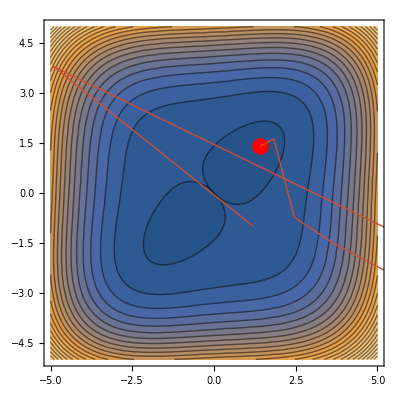

```mathematica
NewtonMethod[f,x0,ϵ]
Grid[res1]
Show[CP,ListLinePlot[X,PlotStyle->Thick,ColorFunction->"Rainbow"]]
```

```mathematica
NewtonMethodGeneralizedFirst[f_,x0_,ϵ_]:=(
t0=SessionTime[]; 
X={x0};
k=0;
αk=1.;
α=αk;
res2={{"k","x1^(k)","x2^(k)","f((x̄)^(k))","α^(k)","‖∇f((x̄)^(k))‖"},{k,X[[-1,1]],X[[-1,2]],f[X[[-1,1]],X[[-1,2]]],α,Norm[Gr[f,X[[-1]]]]}};
(*Граєнтний метод*)
AppendTo[X,X[[-1]]-Gr[f,X[[-1]]] ];
AppendTo[res2,{k,X[[-1,1]],X[[-1,2]],f[X[[-1,1]],X[[-1,2]]],α,Norm[Gr[f,X[[-1]]]]}];
AppendTo[X,X[[-1]]-Gr[f,X[[-1]]]];
AppendTo[res2,{k,X[[-1,1]],X[[-1,2]],f[X[[-1,1]],X[[-1,2]]],α,Norm[Gr[f,X[[-1]]]]}];
While[Norm[Gr[f,X[[-1]]]]≥ϵ,{
If[k>100,Break[]];
temp=X[[-1]]-  α Inverse[H[f,X[[-1]]]].Gr[f,X[[-1]]];
If[f[X[[-1,1]],X[[-1,2]]]≥ f[temp[[1]],temp[[2]]],{
AppendTo[X,temp];
k++;
AppendTo[res2,{k,X[[-1,1]],X[[-1,2]],f[X[[-1,1]],X[[-1,2]]],α,Norm[Gr[f,X[[-1]]]]}];
α=αk;
Continue[];
},{
α/=2;
Continue[];
}
];
}];
t1=SessionTime[];
point={min[[2,1,2]],min[[2,2,2]]};
Print["Час роботи методу: ",t=t1-t0, "\nНев'язка: ",Norm[point-X[[-1]] ],"\nПохибка: ",Abs[f[point[[1]],point[[2]]]-f[X[[-1,1]],X[[-1,2]]]]];
Return[Print["Отримане значення: ",X[[-1]]]];)
```

```mathematica
NewtonMethodGeneralizedFirst[f,x0,ϵ]
Grid[res2]
Show[CP,ListLinePlot[X,PlotStyle->Thick,ColorFunction->"Rainbow"]]
```

Час роботи методу: 0.0070801
Нев'язка: 2.21085×10^-9
Похибка: 0.

Отримане значення: {1.41421,1.41421}

k | x1^(k) | x2^(k) | f((x̄)^(k)) | α^(k) | ‖∇f((x̄)^(k))‖
0 | 1.2 | -1. | 2.9936 | 1. | 7.77152
0 | -4.912 | 3.8 | 788.189 | 1. | 520.274
0 | 464.702 | -220.136 | 4.89817×10^10 | 1. | 4.03666×10^8
1 | 309.802 | -146.756 | 9.67539×10^9 | 1. | 1.19605×10^8
2 | 206.535 | -97.8358 | 1.91118×10^9 | 1. | 3.54384×10^7
3 | 137.69 | -65.2213 | 3.77515×10^8 | 1. | 1.05002×10^7
4 | 91.7944 | -43.4771 | 7.45696×10^7 | 1. | 3.11116×10^6
5 | 61.1976 | -28.9791 | 1.47293×10^7 | 1. | 921814.
6 | 40.8003 | -19.3108 | 2.90924×10^6 | 1. | 273121.
7 | 27.2031 | -12.8611 | 574558. | 1. | 80919.2
8 | 18.1397 | -8.55473 | 113445. | 1. | 23972.2
9 | 12.0996 | -5.67389 | 22387.1 | 1. | 7100.31
10 | 8.0763 | -3.73767 | 4412.04 | 1. | 2102.02
11 | 5.39943 | -2.42071 | 866.536 | 1. | 621.543
12 | 3.62399 | -1.49256 | 168.36 | 1. | 183.159
13 | 2.45971 | -0.73732 | 30.9667 | 1. | 53.3177
14 | 1.8305 | 1.63067 | -5.66129 | 1. | 11.2476
15 | 1.51646 | 1.46027 | -7.88637 | 1. | 2.11475
16 | 1.42265 | 1.41748 | -7.99929 | 1. | 0.160029
17 | 1.41428 | 1.41424 | -8. | 1. | 0.00120725
18 | 1.41421 | 1.41421 | -8. | 1. | 7.00607×10^-8

-Graphics-

```mathematica
NewtonMethodGeneralizedSecond[f_,x0_,ϵ_]:=(
t0=SessionTime[]; 
X={x0};
k=0;
αk=1.;
α=αk;
res3={{"k","x1^(k)","x2^(k)","f((x̄)^(k))","α^(k)","‖∇f((x̄)^(k))‖"},{k,X[[-1,1]],X[[-1,2]],f[X[[-1,1]],X[[-1,2]]],α,Norm[Gr[f,X[[-1]]]]}};
While[Norm[Gr[f,X[[-1]]]]≥ϵ,{
If[k>100,Break[]];
p=-   Inverse[H[f,X[[-1]]]].Gr[f,X[[-1]]];
ff[Α_]=f[X[[-1,1]]+Α p[[1]],X[[-1,2]]+Α p[[2]]];
(*шукаємо аналітичний розв'язок одновимірної задачі безумовної оптимізації методом Ейлера (використовуючи необхідну та достатні умови екстремума)*)

tempΑ =NSolve[D[ff[Α],Α]==0,Α,Reals][[1;;-1,1,2]];
resΑ=αk;
For[i=1,i≤Length[tempΑ],i++,{
If[(D[ff[Α],{Α,2}]/.Α->tempΑ[[i]]) >0,{
resΑ=tempΑ[[i]];
Break[];
}]
}];
α=resΑ;
temp=X[[-1]]-  α Inverse[H[f,X[[-1]]]].Gr[f,X[[-1]]];
AppendTo[X,temp];
k++;
AppendTo[res3,{k,X[[-1,1]],X[[-1,2]],f[X[[-1,1]],X[[-1,2]]],α,Norm[Gr[f,X[[-1]]]]}];
Continue[];
}];

t1=SessionTime[];
point={min[[2,1,2]],min[[2,2,2]]};
Print["Час роботи методу: ",t=t1-t0, "\nНев'язка: ",Norm[point-X[[-1]] ],"\nПохибка: ",Abs[f[point[[1]],point[[2]]]-f[X[[-1,1]],X[[-1,2]]]]];
Return[Print["Отримане значення: ",X[[-1]]]];)
```

```mathematica
NewtonMethodGeneralizedSecond[f,x0,ϵ]
Grid[res3]
Show[CP,ListLinePlot[X,PlotStyle->Thick,ColorFunction->"Rainbow"]]
```

Час роботи методу: 0.008118
Нев'язка: 2.62224×10^-6
Похибка: 7.03722×10^-11

Отримане значення: {1.41421,1.41422}

k | x1^(k) | x2^(k) | f((x̄)^(k)) | α^(k) | ‖∇f((x̄)^(k))‖
0 | 1.2 | -1. | 2.9936 | 1. | 7.77152
1 | 0.052266 | 0.518769 | -0.579728 | 3.48773 | 2.86229
2 | 1.45683 | 1.14363 | -7.3098 | -3.53467 | 4.83649
3 | 1.4399 | 1.42084 | -7.99355 | 0.748955 | 0.499445
4 | 1.41421 | 1.41422 | -8. | 1.02276 | 0.0000546945

-Graphics-